## DanglingEdges-example.nb DanglingEdges, DanglingVertices

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 18:46:12
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

```mathematica
v={{0,0}, {2, 0}, {1, 2}, {2, 1}, {2, 2}};
e={{1,2},  {2, 3}, {3, 1}, {3, 4}}; 
c={{1,2,3}}; 
q=Tissue[v,e,c]
```

Tissue[{{0,0},{2,0},{1,2},{2,1},{2,2}},{{1,2},{2,3},{3,1},{3,4}},{{1,2,3}}]

```mathematica
DanglingEdges[q]
```

{4}

```mathematica
DanglingVertices[q]
```

{5}

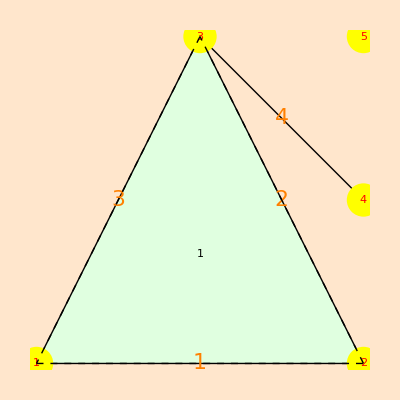

```mathematica
ShowTissue[q, "Vertices"-> {Yellow, PointSize[.06]}, "VertexNumbers"->{Red, FontSize-> 20}, "CellNumbers"-> True , "EdgeNumbers"-> True,
"EdgeNumberStyle"-> {Orange, FontSize-> 22}, 
 "All"-> True , "BoundaryStyle"-> Dashed, Background-> LightOrange]
```